```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

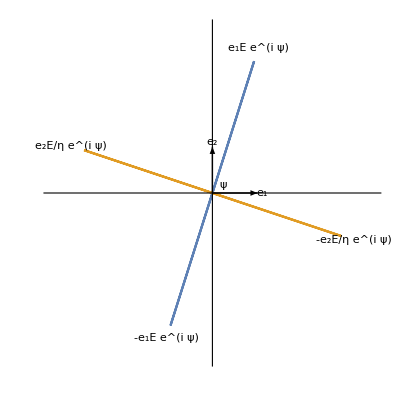

```mathematica
ClearAll[p1, bold, pt]
pt[r_, t_] := r{Cos[t],Sin[t]};
bold = Style[ #, Bold] &;

p1 = Module[{e1,e2, psi, r,o, vecE, te1, te2, vecH, rho},
{e1,e2} = IdentityMatrix[2];
psi = .4 Pi;
rho = 3;
r = rho{-1.2,1.2};
o = {0,0};
vecE = pt[rho,psi] ;
vecH = pt[rho,psi + Pi/2];
te1 = Subscript["e"// bold, 1];
te2 = Subscript["e"// bold, 2];
Show[
{
Graphics[
ParametricPlot[{vecE Cos[ t ],vecH Cos[ t ]}, {t, 0, 2 Pi}, 
PlotRange -> {r,r},
Ticks -> None
]
,AspectRatio-> 1
]
}
,
Graphics[{
Arrow[{o, e1}],
Arrow[{o, e2}],
Text[te1, 1.1 e1],
Text[te2, 1.1 e2],
Text[Row[{te1, "E e^(i ψ)"}], 1.1 vecE],
Text[Row[{"-", te1, "E e^(i ψ)"}], -1.1 vecE],
Text[Row[{te2, "E/η e^(i ψ)"}], 1.1 vecH],
Text[Row[{"-", te2, "E/η e^(i ψ)"}], -1.1 vecH],
Text[ "ψ", pt[0.3,psi/2]]
}
,BaseStyle->14 
]
]
]
```

```mathematica
peeters`exportForLatex["linearPolarizationFig1", p1]
```

{linearPolarizationFig1.eps,linearPolarizationFig1pn.png}